```mathematica
ClearAll[f0,m1,m2,mchirp,M,r,d];
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
M=mchirp[m1,m2]*4.92549095*10^-6;
d=r*1.0292712503*10^8;
tmerg[M_,f0_]=5(256(N[π]f0)^(8/3)M^(5/3))^-1;
F[M_,f0_,t_]=(M (f0)^9)^(1/8)((M f0)^(1/3)-256f0^3 M^2N[π]^(8/3)(t/5))^(-3/8);
Angle[M_,f0_,t_]=-2((256(N[π]M f0)^(8/3))^(-1)-(t/(5M)))^(5/8);
Amplitude[M_,f0_,d_,t_]=4M^(5/3)N[π]^(2/3)(F[M,f0,t])^(2/3)d^(-1 );
```

```mathematica
m1=10;
m2=10;
f0=10;
r= 8*10^3;
```

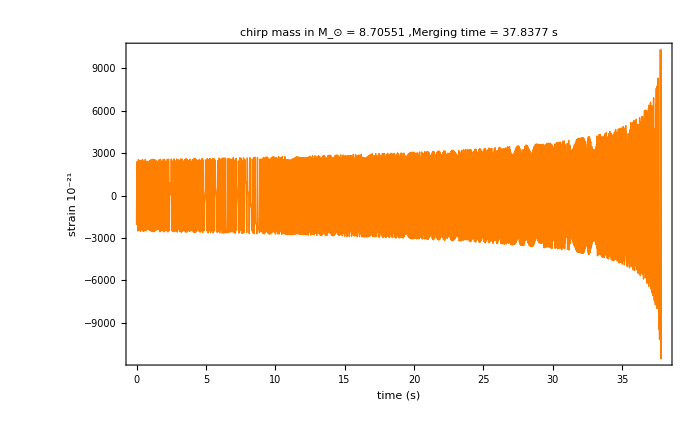

```mathematica
g1=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*10^21} ,{t,0,tmerg[M,f0]},
PlotStyle->{Orange},Frame->True,ImageSize->700,BaseStyle ->{FontFamily->"Arial",16},PlotLabel->Row[{"chirp mass in ",Subscript[Style["M", Italic],"⊙"]," = ",  N[mchirp[m1,m2]],"   ,Merging time = ",  tmerg[M,f0]"s"}],FrameLabel->{"time (s)",(Subsuperscript["10","","-21"] )" strain " }]
```

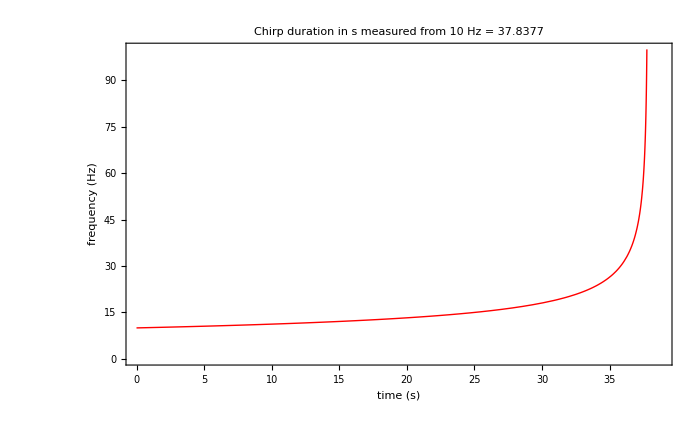

```mathematica
g2=Plot[F[M,f0,t],{t,0,tmerg[M,f0]}, PlotStyle->{Red},Frame->True,ImageSize->700,BaseStyle ->{FontFamily->"Arial",16},PlotRange->{{0,tmerg[M,f0]+1},{0,100}}
 ,PlotLabel->Row[{"Chirp duration in s measured from " , f0," Hz = ",tmerg[M,f0]}],FrameLabel->{"time (s)","frequency (Hz)"}]
```